# Hydrogen diffusion in Stainless steel

Author : Erdong Wang
Mar .20 th 2017
Simulation the hydrogen diffusion in SS while baking and post baking

## Modeling

```mathematica
SetDirectory["/Users/wange/Documents/Research/eRHIC gun/eRHIC baseline/Vacuum"]
Directory[]
```

/Users/wange/Documents/Research/eRHIC gun/eRHIC baseline/Vacuum

/Users/wange/Documents/Research/eRHIC gun/eRHIC baseline/Vacuum

```mathematica
Remove["Global`*"]
```

### Initial condition; modeling

```mathematica
SetDirectory["/Users/wange/Documents/Research/eRHIC gun/eRHIC baseline/Vacuum"];
thickness=0.3;(*cm*)
step=0.002;(*cm,WZ in paper, with of zone or separation between points in cm*)
mesh=thickness/step;(*N, *)
concen=0.3;(*Torr.L at 0°C/cm3*)
diffco0=0.012 ;(*cm^2/s*)
ed=14500 4.183/(6.022 10^23);(*cal/mol; 0.57eV*)
kb=1.380648 10^-23;(*J/K*)
diffconst[t_]:=diffco0 ⅇ^(-ed/(kb (t+273)));
diffconst900=6.254 10^-5;(*cm^2/s,DC in paper*)
diffco=diffconst[450];
tstep=0.01;(*time step s,NS in paper seconds per time interval*)
initm=Table[concen,{mesh}];
ti=diffco tstep/step^2;(*cm^2/s.s/cm^2=1,diffusion in a step time, T in paper*)
qdc=ti step/tstep;
recombco950=6 10^-22;(*[atom/s cm^2]/[atom/cm^3]^2=cm^4/(atom s)*)
recombco=recombco950;
convt=2 2.686763 10^19;(*To convert the concentration from cm^3[STP]/cm^3 to atom/cm^3,multiply by 2 atom/molecule and by 2.686763?1019 molecule/cm3*)
initma=initm;(*initial concentrate distribution*)

finfc[bkur_]:=(
savedata={Join[{0},{0},{0},{0},{0},initma]};
newm=initma;
For[i=1,i<bkur/tstep,i++,

delm=(newm[[#-1]]+newm[[#+1]]-2newm[[#]]) ti&/@Range[2,Length[newm]-1];
qd=(newm[[2]]-newm[[1]])qdc convt;(*STP cm^3/(s cm^2)atom/cm^3=atom/(s cm^2)*)
outgs=recombco (newm[[1]] convt)^2;(*atom/(s cm^2)*)
(*dels={(qd-outgs)/convt/qdc };*)
outgstorr=outgs/convt;
dels={(qd-outgs) tstep/convt/step};
(*qdo=(newm[[-1]]-newm[[-2]])qdc convt;
delo={-qdo  tstep/convt/step };
Print[qd," ",outgs," ",dels," ",newm[[1]] convt];*)
newm=newm+Join[dels,delm,dels];
(*Print[Catenate[Join[{{i tstep}},{{outgs}},{{qd}},{newm}]]];*)
fo=4 diffco i tstep/thickness^2;(*Demtionless number for estimate baking efficiency *)
newdata=Join[{i tstep},{outgs},{outgstorr},{qd},{fo},newm];
(*sarr={0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.2,0.3,0.4,0.5,1.,10.,30.,50.,100.,200.,500.,1000.,2000.,3000.,5000.,10000.,20000.,30000.,50000.,100000.};*)
sarr={0.01,0.1,0.5,1.,10.,30.,50.,100.,200.,500.,1000.,2000.,3600.,5000.,10000.,20000.,30000.,50000.,100000.,200000.,300000.,360000.};
If[
MemberQ[sarr,newdata[[1]]],
Print[MemberQ[sarr,newdata[[1]]],newdata[[1]]];
savedata=Append[savedata,newdata];
];
];
Return[newdata];
)
```

### Result

savedata6m: 6mm thickness, with 900 C bake for 5500s(diffco=6.254 10^-5,recombco=6 10^-22;)
savedata3m: 3mm thickness, with 900 C bake for 5500s(diffco=6.254 10^-5,recombco=6 10^-22;)
savedata4m: 4mm thickness, with 900 C bake for 5500s(diffco=6.254 10^-5,recombco=6 10^-22;)
savedata4m: 5mm thickness, with 900 C bake for 5500s(diffco=6.254 10^-5,recombco=6 10^-22;)
savedata30m: 3cm thickness, with 900 C bake for 5500s(diffco=6.254 10^-5,recombco=6 10^-22;)

```mathematica
finfc[360005]
savedata3m=savedata;
```

True0.01

True0.1

True0.5

True1.

True10.

True30.

True50.

True100.

True200.

True500.

True1000.

True2000.

True3600.

True5000.

True10000.

True20000.

True30000.

True50000.

$Aborted

```mathematica
Export["savedata_3mm_450.dat",savedata3m];
```

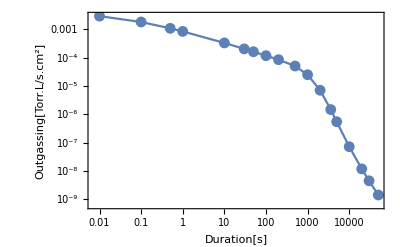

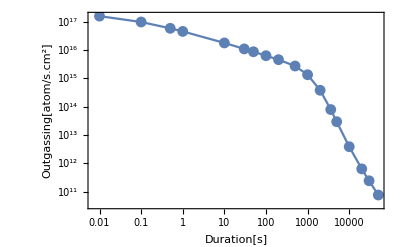

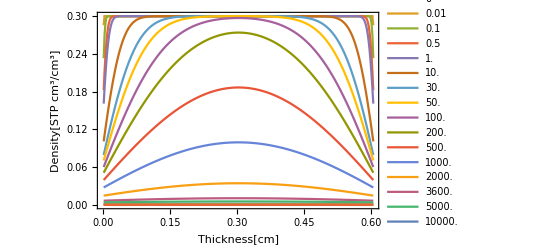

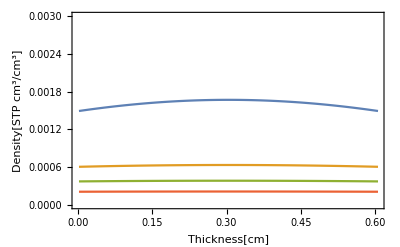

```mathematica
ListLogLogPlot[{savedata[[;;,1]][[#]],savedata[[;;,3]][[#]]}&/@Range[Length[savedata[[;;,1]]]],Joined->True,Mesh->All,Frame->True,FrameLabel->{"Duration[s]","Outgassing[Torr.L/s.cm^2]"}]
ListLogLogPlot[{savedata[[;;,1]][[#]],savedata[[;;,2]][[#]]}&/@Range[Length[savedata[[;;,1]]]],Joined->True,Mesh->All,Frame->True,FrameLabel->{"Duration[s]","Outgassing[atom/s.cm^2]"}]
ListPlot[savedata[[All,6;;]],Joined->True,DataRange->step {1,Length[savedata[[1]]-5]},PlotRange->All,Frame->True,PlotLegends->savedata[[All,1]],FrameLabel->{"Thickness[cm]","Density[STP cm^3/cm^3]"}]
ListPlot[savedata[[All,6;;]],Joined->True,DataRange->step {1,Length[savedata[[1]]-5]},PlotRange->{0,0.003},Frame->True,FrameLabel->{"Thickness[cm]","Density[STP cm^3/cm^3]"}]
```

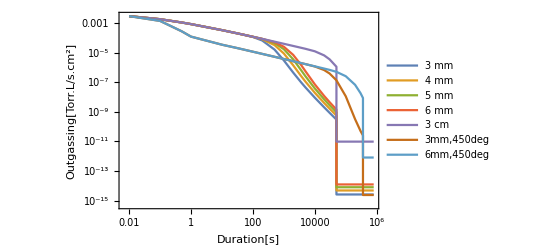

```mathematica
savedata3m=Import["savedata_3mm.dat"];
savedata4m=Import["savedata_4mm.dat"];
savedata5m=Import["savedata_5mm.dat"];
savedata6m=Import["savedata_6mm.dat"];
savedata30m=Import["savedata_30mm.dat"];
savedata3m450d=Import["savedata_3mm_450.dat"];
savedata6m450d=Import["savedata_6mm_450.dat"];
ListLogLogPlot[{{savedata3m[[;;,1]][[#]],savedata3m[[;;,3]][[#]]}&/@Range[Length[savedata3m[[;;,1]]]],
{savedata4m[[;;,1]][[#]],savedata4m[[;;,3]][[#]]}&/@Range[Length[savedata4m[[;;,1]]]],
{savedata5m[[;;,1]][[#]],savedata5m[[;;,3]][[#]]}&/@Range[Length[savedata5m[[;;,1]]]],
{savedata6m[[;;,1]][[#]],savedata6m[[;;,3]][[#]]}&/@Range[Length[savedata6m[[;;,1]]]],{savedata30m[[;;,1]][[#]],savedata30m[[;;,3]][[#]]}&/@Range[Length[savedata30m[[;;,1]]]],
{savedata3m450d[[;;,1]][[#]],savedata3m450d[[;;,3]][[#]]}&/@Range[Length[savedata3m450d[[;;,1]]]],
{savedata6m450d[[;;,1]][[#]],savedata6m450d[[;;,3]][[#]]}&/@Range[Length[savedata6m450d[[;;,1]]]]
},Joined->True,Frame->True,
FrameLabel->{"Duration[s]","Outgassing[Torr.L/s.cm^2]"},GridLines->{Flatten[Table[n,{n,1 #,9 #,1 #}]&/@(10^Range[-3,5])],Flatten[Table[n,{n,1 #,9 #,1 #}]&/@(10^Range[-15,-3])]},PlotRange->All,

GridLinesStyle->LightGray,PlotLegends->{"3 mm","4 mm","5 mm","6 mm","3 cm","3mm,450deg","6mm,450deg"}]
```

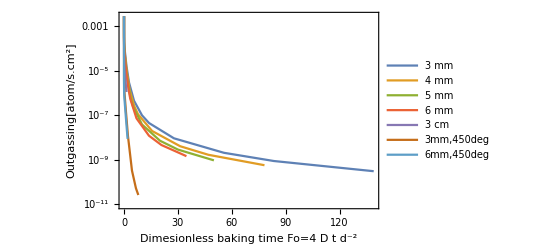

```mathematica
ListLogPlot[{{savedata3m[[;;,5]][[#]],savedata3m[[;;,3]][[#]]}&/@Range[Length[savedata3m[[;;,1]]]],
{savedata4m[[;;,5]][[#]],savedata4m[[;;,3]][[#]]}&/@Range[Length[savedata4m[[;;,1]]]],
{savedata5m[[;;,5]][[#]],savedata5m[[;;,3]][[#]]}&/@Range[Length[savedata5m[[;;,1]]]],
{savedata6m[[;;,5]][[#]],savedata6m[[;;,3]][[#]]}&/@Range[Length[savedata6m[[;;,1]]]],{savedata30m[[;;,5]][[#]],savedata30m[[;;,3]][[#]]}&/@Range[Length[savedata30m[[;;,1]]]],
{savedata3m450d[[;;,5]][[#]],savedata3m450d[[;;,3]][[#]]}&/@Range[Length[savedata3m450d[[;;,1]]]],
{savedata6m450d[[;;,5]][[#]],savedata6m450d[[;;,3]][[#]]}&/@Range[Length[savedata6m450d[[;;,1]]]]
},Joined->True,Frame->True,
FrameLabel->{"Dimesionless baking time Fo=4 D t d^-2","Outgassing[atom/s.cm^2]"},GridLines->{Table[n,{n,0,140,20}],Flatten[Table[n,{n,1 #,9 #,1 #}]&/@(10^Range[-11,-3])]},PlotRange->All,

GridLinesStyle->LightGray,PlotLegends->{"3 mm","4 mm","5 mm","6 mm","3 cm","3mm,450deg","6mm,450deg"}]
```